# Derivation of scattering from Thin Disks

## Thin circular disk

```mathematica
$Assumptions:={R>0, q>0,r>0,Sin[θq]>= 0,θq> 0,θq<= π/2}
```

Lets assume the disk is in the xy plane, then any scatterer point is given in polar coordinates by r [0:R], ϕ in [-π:π]

```mathematica
Rvec:={r Cos[ϕ],r Sin[ϕ],0}
```

where the measure is r dr dϕ  when integrating in polar coordinates.
The q vector can hit the disk from any direction on a sphere, but due to symmetry we can put the qvector in upper xz plane, using the angle θp that the q vector makes with the z axis. The proper measure is d cos[θp] dϕp = Sin[θq] dθq dϕp. Due to rotation symmetry around z, the ϕq integral gives a 2π constant, that is cancelled by the corresponding normalization constant, and hence can be neglected.

```mathematica
qvec:={q Sin[θq],0,q Cos[θq]}
```

```mathematica
Rvec.qvec
```

q r Cos[ϕ] Sin[θq]

To normalize, we need this integral, which happens to be the area of the disk:

```mathematica
Integrate[r,{r,0,R},{ϕ,-π,π}]
```

π R^2

Then form factor amplitude relative to the centre of the disk for a given FIXED q vector is: (where r comes from the measure in polar coordinates, and π R.b2 from the normalization.

```mathematica
Aqvec=Integrate[Exp[-I Rvec.qvec] r/(π R^2),{r,0,R},{ϕ,-π,π}]//FunctionExpand
```

(2 BesselJ[1,q R Sin[θq]] Csc[θq])/(q R)

This expression is for a FIXED q vector that makes an angle of θq with the z axis. Hence we need to average over all the incoming q vectors, the measure is Sin[θq] dθq  and we integrate from [0:π/2] corresponding from the north pole (z axis) down to the equator: (this average contribute a normalization constant of 1)

```mathematica
Integrate[Sin[θq],{θq,0,π/2}]
```

1

```mathematica
Adiskcenter=Integrate[Aqvec Sin[θq],{θq,0,π/2}]
```

∫_0^(π/2) (2 BesselJ[1,q R Sin[θq]])/(q R)ⅆθq

```mathematica
Adiskcenter/.q-> x/R
```

∫_0^(π/2) (2 BesselJ[1,x Sin[θq]])/x ⅆθq

There is no closed analytic form for this form factor amplitude.
To calculate the form factor of a disk, we recognize that the vector between any two scatterers a,b R=Rb-Ra in the disk, can be written as R=Rb-0-(Ra-0), where 0 is the centre of the disk. Hence the pair distance between the two scatterers is the convolution of two radial distance distributions. Aqvec above is the Fourier transformation this radial distribution for fixed geometry. Fourier transforming the convolution of two identical distributions becomes the square of the Fourier transform Fqvec=Aqvec^2, which is the form factor of a disk in fixed geometry. What remains is to perform the orientational average of the angle between the q vector and  the disk:

```mathematica
Fdisk=Integrate[Aqvec^2 Sin[θq],{θq,0,π/2}]
```

(2 q R-2 BesselJ[1,2 q R])/(q^3 R^3)

```mathematica
Fdisk/.q-> x/R
```

(2 x-2 BesselJ[1,2 x])/x^3

Reference for form factor of thin disk : O . Kratky and G . Porod, J . Colloid . Sci . 4, 35 (1949) .

#### Distributed surface reference point .

The form factor amplitude of a scatterer on the disk relative to a randomly chosen point  on the disk is identical to the form factor above, similar the phase factor between two randomly chosen points.

#### Circular rim

A special case of the disk, is where we just consider the rim, which forms a circle.
First the normalization constant, which is its circumference.

```mathematica
Integrate[R,{ϕ,-π,π}]
```

2 π R

Form factor amplitude of circular rim in fixed geometry:

```mathematica
Arimqvec=Integrate[Exp[-I Rvec.qvec] R/(2 π R)/.r-> R,{ϕ,-π,π}]
```

BesselJ[0,q R Sin[θq]]

Making an orientational average of a circle produces the form factor amplitude of a spherical shell:

```mathematica
Psicenter2rim=Integrate[Arimqvec Sin[θq],{θq,0,π/2}]//FunctionExpand
```

Sin[q R]/(q R)

With this we can now calculate the form factor of a circular rim, which is the same as the form factor amplitude of the rim relative to a random point, and the phase factor between two randomly chosen points on the rim :

```mathematica
Psirim2rim=Integrate[(Arimqvec)^2 Sin[θq],{θq,0,π/2}]//Expand
```

BesselJ[0,2 q R]+1/2 π BesselJ[1,2 q R] StruveH[0,2 q R]-1/2 π BesselJ[0,2 q R] StruveH[1,2 q R]

We can also derive the form factor amplitude of a random scatterer on a disk relative to a random point on its rim, which is also the rim-to-disk surface phase factor :

```mathematica
Adiskrim=Integrate[Aqvec Arimqvec Sin[θq],{θq,0,π/2}]//Expand
```

∫_0^(π/2) (2 BesselJ[0,q R Sin[θq]] BesselJ[1,q R Sin[θq]])/(q R)ⅆθq

Not many expression here that are easy to evaluate numerically. The derivation reproduce results of C. Svaneborg and J.S. Pedersen  “A formalism for scattering of complex composite structures. II. Distributed reference points” J. Chem. Phys. 136, 154907 (2012); doi: 10.1063/1.3701737

#### Plots

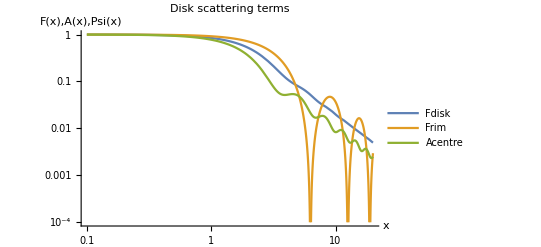

```mathematica
LogLogPlot[{Fdisk,Adiskcenter,Adiskrim}/.q->x/R//Evaluate,{x,0.1,20},PlotLabel-> "Disk scattering terms",AxesLabel-> {"x","F(x),A(x),Psi(x)"},PlotLegends->{"Fdisk","Frim","Acentre","Arimdisk"},PlotRange-> {0.0001,1}]
```

#### Guinier - expansion

Above we derived the mean - square distances explicitly. Here we show how to obtain these from a Guinier expansion of the various scattering terms.

The Guinier expansion of F is
1 - q^2 Rg^2 / 3 + O(q^4)

```mathematica
Series[F,{q,0,3}]
```

1-(R^2 q^2)/6+O[q]^4

Hence to isolate the radius of gyration in the series:

```mathematica
Series[Fdisk,{q,0,3}]
Solve[Normal[%]==1-(Rg2 q^2)/3,Rg2]//Simplify
```

1-(R^2 q^2)/6+O[q]^4

{{Rg2→R^2/2}}

```mathematica
Series[Fdisk,{q,0,3}]
Solve[Normal[%]==1-(σR2 q^2)/6,σR2]//Simplify
```

1-(R^2 q^2)/6+O[q]^4

{{σR2→R^2}}

```mathematica
Series[Adiskcenter,{q,0,3}]
Solve[Normal[%]==1-(σR2 q^2)/6,σR2]//Simplify
```

1-(R^2 q^2)/12+O[q]^4

{{σR2→R^2/2}}

#### Save example data to file for Validation :

```mathematica
Clear[PARENTDIR,DIR1,DIRO1]
PARENTDIR=Directory[]
DIR1:=PARENTDIR<>"/Sampled/ThinDisk_R1/"
DIRO1:=PARENTDIR<>"/../Examples/Validation/ThinDisk_R1/"
CreateDirectory[DIRO1];
```

/home/zqex/source/SEB/Mathematica

CreateDirectory::eexist: /home/zqex/source/SEB/Examples/Validation/ThinDisk_R1/ already exists.

```mathematica
SaveFunction[func_,filename_,NN_,qmin_,qmax_]:=Module[{},Export[filename,{#,N[func[#]]}&/@Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]]]
SetAttributes[SaveFunction,HoldAll]
```

```mathematica
Clear[qvec,qq]
qvec[qmin_,qmax_,NN_]:=Table[10^(Log[10,qmax/qmin]*i/NN+Log[10,qmin]),{i,0,NN}]
qq:=qvec[0.8,50,500]//N
```

```mathematica
Form factor :
```

(2 q R-2 BesselJ[1,2 q R])/(q^3 R^3)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/ThinDisk_R1/FF.dat

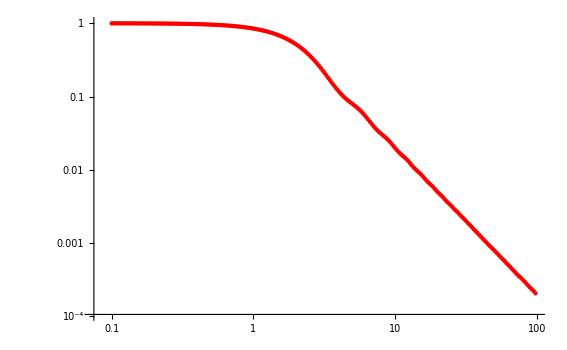

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Fdisk
Func1[q_]:=Term[q]/.R-> 1
FILE="F.q";
OFILE=DIRO1<>"FF.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

```mathematica
Form factor amplitude (center):
```

∫_0^(π/2) (2 BesselJ[1,q R Sin[θq]])/(q R)ⅆθq

/home/zqex/source/SEB/Mathematica/../Examples/Validation/ThinDisk_R1/FFA_center.dat

NIntegrate::precw: The precision of the argument function (2.5 BesselJ[1,0.8 Sin[θq]]) is less than WorkingPrecision (26.).

NIntegrate::precw: The precision of the argument function (2.47941 BesselJ[1,0.806644 Sin[θq]]) is less than WorkingPrecision (26.).

NIntegrate::precw: The precision of the argument function (2.45899 BesselJ[1,0.813343 Sin[θq]]) is less than WorkingPrecision (26.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

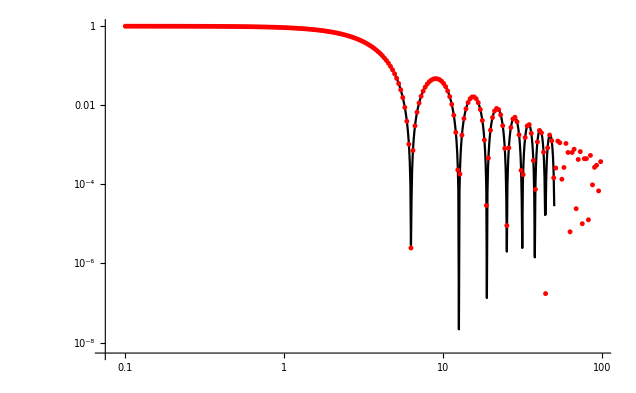

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Adiskcenter
Func1[q_]:=Term[q]/.R-> 1
FILE="FFA_center.q";
OFILE=DIRO1<>"FFA_center.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

```mathematica
Form factor amplitude (rim):
```

```mathematica
Adiskrim
```

∫_0^(π/2) (2 BesselJ[0,q R Sin[θq]] BesselJ[1,q R Sin[θq]])/(q R)ⅆθq

```mathematica
{# ,Abs[Func1[#]]}&/@qq
```

{q Sin[θq],0.,q Cos[θq]}[{0.8,0.806138},{50.,0.00922663},{500.,0.0010047}]

∫_0^(π/2) (2 BesselJ[0,q R Sin[θq]] BesselJ[1,q R Sin[θq]])/(q R)ⅆθq

/home/zqex/source/SEB/Mathematica/../Examples/Validation/ThinDisk_R1/FFA_rim.dat

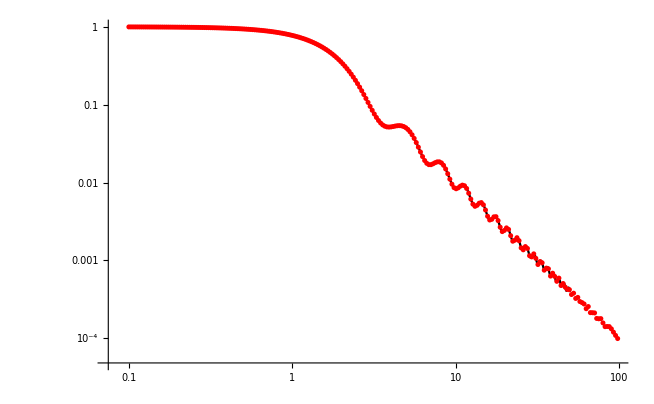

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Adiskrim
Func1[q_]:=Term[q]/.R-> 1/.r->1//N
FILE="FFA_rim.q";
OFILE=DIRO1<>"FFA_rim.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

```mathematica
Phase factor rim-to-rim:
```

BesselJ[0,2 q R]+1/2 π BesselJ[1,2 q R] StruveH[0,2 q R]-1/2 π BesselJ[0,2 q R] StruveH[1,2 q R]

/home/zqex/source/SEB/Mathematica/../Examples/Validation/ThinDisk_R1/Psi_rim2rim.dat

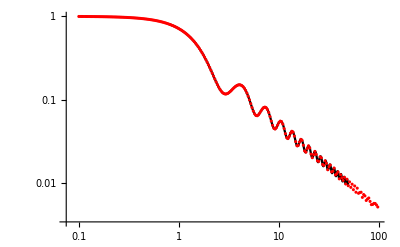

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Psirim2rim
Func1[q_]:=Term[q]/.R-> 1/.r->1
FILE="P_rim2rim.q";
OFILE=DIRO1<>"Psi_rim2rim.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
DATA={#[[1]] ,Abs[#[[2]]]}&/@ Delete[Import[DIR1<>FILE,"Table"],1];
ListLogLogPlot[{DATA,{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

```mathematica
Phase factor center-to-rim:
```

Sin[q R]/(q R)

/home/zqex/source/SEB/Mathematica/../Examples/Validation/ThinDisk_R1/Psi_center2rim.dat

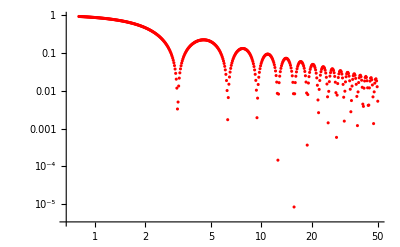

```mathematica
Clear[Term,Func1,DATA]
Term[q_]=Psicenter2rim
Func1[q_]:=Term[q]/.R-> 1/.r->1
OFILE=DIRO1<>"Psi_center2rim.dat"
SaveFunction[Func1,OFILE,200,0.01,50];
ListLogLogPlot[{{# ,Abs[Func1[#]]}&/@qq},PlotStyle->{{Red,Thick},Black},Joined-> {False,True}]
```

#### Size estimations:

```mathematica
Series[Fdisk,{q,0,3}];
Solve[Normal[%]==1-(Rg2 q^2)/3,Rg2]//Simplify;
Rg2/.%[[1]]
```

R^2/2

```mathematica
Series[Adiskcenter,{q,0,3}];
Solve[Normal[%]==1-(sigmaR2 q^2)/6,sigmaR2]//Simplify;
sigmaR2/.%[[1]]
```

R^2/2

```mathematica
Series[Fdisk,{q,0,3}];
Solve[Normal[%]==1-(sigmaR2 q^2)/6,sigmaR2]//Simplify;
sigmaR2/.%[[1]]
```

R^2

```mathematica
Arim
```

∫_0^(π/2) (2 BesselJ[0,x Sin[θq]] BesselJ[1,x Sin[θq]])/x ⅆθq

```mathematica
Series[(2 BesselJ[0,x Sin[θq]] BesselJ[1,x Sin[θq]])/x/.x-> q R,{q,0,5}]
```

Sin[θq]-3/8 (R^2 Sin[θq]^3) q^2+5/96 R^4 Sin[θq]^5 q^4+O[q]^6

```mathematica
Integrate[Sin[θq]-3/8 (R^2 Sin[θq]^3) q^2+5/96 R^4 Sin[θq]^5 q^4,{θq,0,π/2}]//Expand
```

1-(q^2 R^2)/4+(q^4 R^4)/36

```mathematica
Solve[1-(q^2 R^2)/4==1-(sigmaR2 q^2)/6,sigmaR2]//Simplify;
sigmaR2/.%[[1]]
```

(3 R^2)/2

```mathematica
Series[Arimcenter,{q,0,3}];
Solve[Normal[%]==1-(sigmaR2 q^2)/6,sigmaR2]//Simplify;
sigmaR2/.%[[1]]
```

r^2

```mathematica
Series[Psirim2rim,{q,0,3}];
Solve[Normal[%]==1-(sigmaR2 q^2)/6,sigmaR2]//Simplify;
sigmaR2/.%[[1]]
```

2 r^2